```mathematica
Y10[l_,θ1_,θ2_,ϕ1_,ϕ2_]:=Sum[ClebschGordan[{l,m},{l,-m},{1,0}]SphericalHarmonicY[l,m,θ1,ϕ1]SphericalHarmonicY[l,-m,θ2,ϕ2],{m,-l,l}];
```

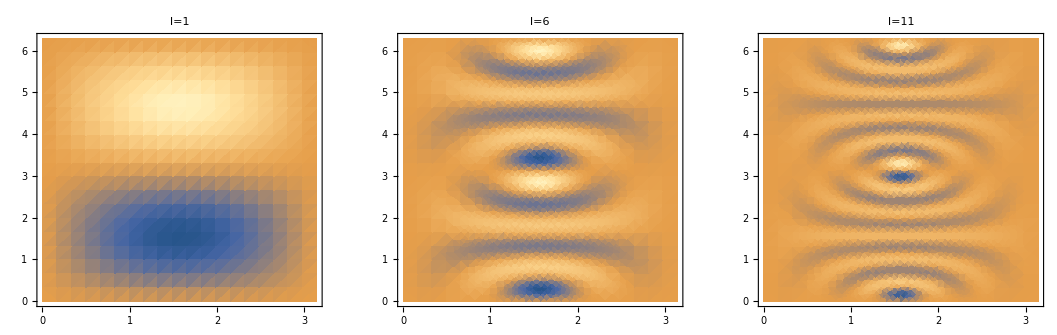

```mathematica
GraphicsRow[Table[DensityPlot[Im[Y10[l,π/2,θ,π,ϕ]],{θ,0,π},{ϕ,0,2π},PlotLabel->Style["l="<>ToString[l],FontSize->14],PerformanceGoal->"Quality",PlotPoints->20],{l,1,11,5}]]
```